```mathematica
NSolve[Erf[x]-(-1)==0.001,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2.32675}}

```mathematica
f[x_,c_,e_]:=Exp[-(x-c)^2/e];
h[x_,b_]:=0.5*(Erf[1*Abs[x-b]-2.32675]+1);
```

```mathematica
c=1; e=1;b1=0.9; b2=1.2;
```

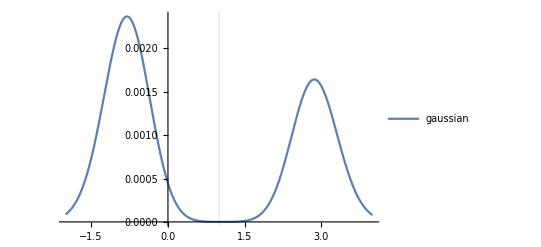

```mathematica
Plot[{f[x,c,e]*h[x,b1]*h[x,b2]},{x,c-3 √e,c+3 √e},GridLines->{{b},{}},
PlotLegends->{"gaussian", "error funciton 3"},PlotRange->Full]
```